## All edges

```mathematica
Column[
Table[
Labeled[
With[
{relevant = Select[Keys[allGraphs3],With[{g=allGraphs3[#,"graph"]},VertexCount[g]==3 && EdgeCount[g]==edges]&]},
TableForm[
Sort[
Tally[
Table[
{Sort[Tally[Map[StringCount[SymbolName[#],"x"]+1&,ListofVars[allGraphs3[k,"colofour"]]]]],Labeled[allGraphs3[k,"graph"],k]},
{k,relevant}
]
,#1[[1]]==#2[[1]]&
]
], TableDepth->1]
],
Style[edges,Red,48,Bold],
Top
],
{edges,0,6}
]
]
```

{{{{1,1},{2,3},{3,1}},-Graphics-0},1}0
{{{{2,2},{3,1}},-Graphics-9},3}1
{{{{2,1},{3,1}},-Graphics-12},3}2
{{{{3,1}},-Graphics-13},1}3
{}4
{}5
{}6

```mathematica
PaintEdges[key_,key2_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=allGraphs[key2, "colofourrealnull"],
form3=Map[ChangeSymbol[#]&,allGraphs[key2,"colofour"]],pairs, vars, blocks=Association[],c,edges,edges2,set, found=Association[],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],nonRoot,   blueEdges, blueVertices, g, edgeSymbols, otherEdges, labels, nodes},
edgeSymbols=Select[ListofVars[form2],StringCount[SymbolName[#],"x"]==2&];
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
g=Graph[vars,edges];
blueEdges=edges2;
blueVertices=Map[#[[2]]&,blueEdges];
otherEdges=Flatten[Join[Table[Descendents[g,{e}],{e,edgeSymbols}]]];
labels=Map[#[[1]]->Style[ #[[2]],Bold]&,Tally[otherEdges]];
nodes=Map[#[[1,1]]-> Part[{Red,Darker[Green],Blue,Darker[Red]},#[[2]]]&,Tally[otherEdges]];
otherEdges=Map[#[[1]]-> Part[{Red,Darker[Green],Blue,Darker[Red]},#[[2]]]&,Tally[otherEdges]];
Graph[vars,edges,
VertexLabels->Table[n->Rotate[SymbolToLabel[n],Pi/4],{n,vars}],
GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->otherEdges,
EdgeLabels->labels,
VertexStyle->Join[nodes,Map[#->Cyan&,blueVertices]],
ImageSize->720]
]
```

```mathematica
allGraphs3[360,"graph"]
```

Missing[KeyAbsent,360]

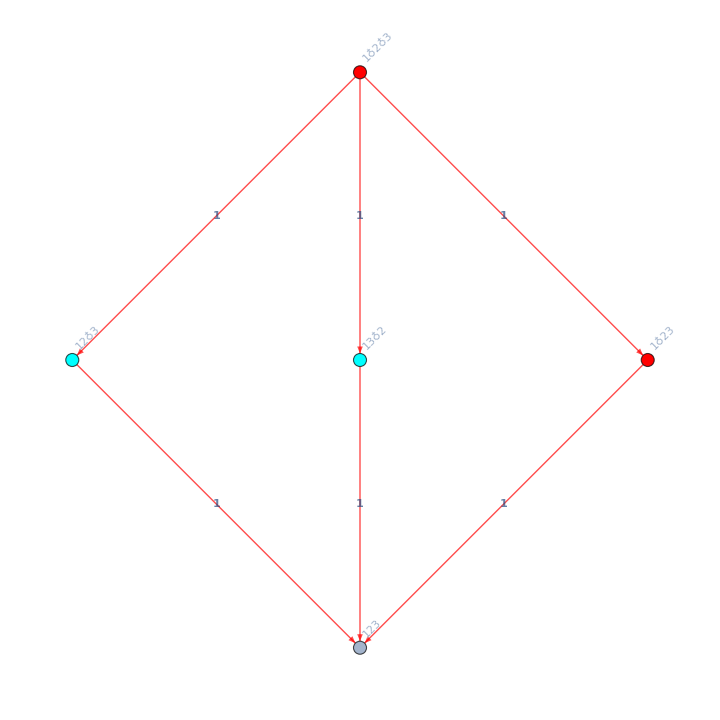

```mathematica
PaintEdges[K3Key, 1, allGraphs3]
```

```mathematica
allGraphs3[328,"graph"]
```

Missing[KeyAbsent,328]

SymbolName::sym: Argument KeyAbsent at position 1 is expected to be a symbol.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[SymbolName[KeyAbsent],v→n].

Symbol::string: String expected at position 1 in Symbol[StringReplace[SymbolName[KeyAbsent],v→n]].

SymbolName::sym: Argument 328 at position 1 is expected to be a symbol.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[SymbolName[328],v→n].

Symbol::string: String expected at position 1 in Symbol[StringReplace[SymbolName[328],v→n]].

SymbolName::sym: Argument Missing[KeyAbsent,328] at position 1 is expected to be a symbol.

General::stop: Further output of SymbolName::sym will be suppressed during this calculation.

StringCount::strse: String or list of strings expected at position 1 in StringCount[SymbolName[Missing[KeyAbsent,328]],x].

{}

First::nofirst: {} has zero length and no first element.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[Missing[KeyAbsent,364]],1].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[StringDrop[SymbolName[Missing[KeyAbsent,364]],1],x→|].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

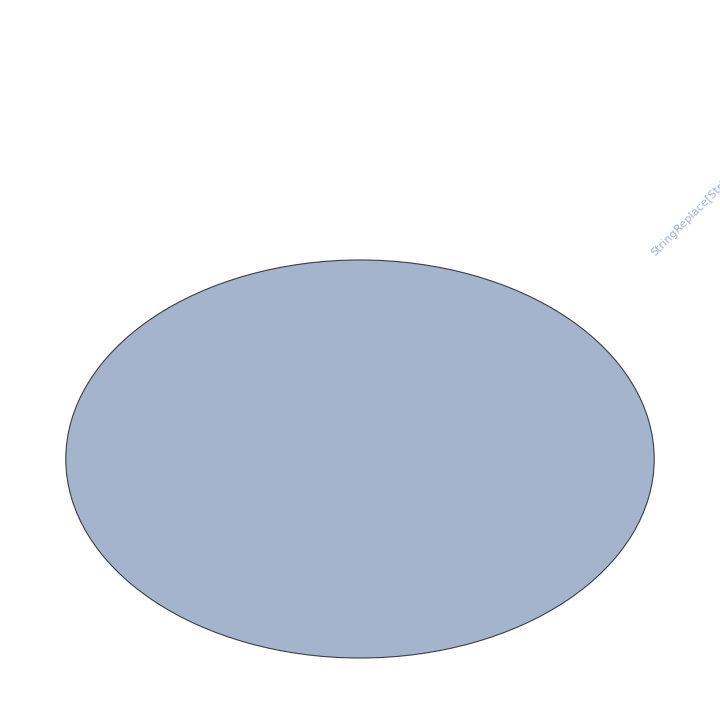

```mathematica
MobiusGraphDoubleGood5[K4Key, 328, allGraphs3]
```